```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

#### Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
(*AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]*)
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifefor4D[model_,fitParams_,x_,y_,z_]:=Module[{numFs,modelvaluej,modelvalue,jackknifeResults, numParams},numFs=Length[fitParams[[1]]];
numParams=Length[fitParams];
modelvaluej[j_]:=Module[{datafitParams},datafitParams=Table[fitParams[[k,j]],{k,numParams}];
model[x,y,z,datafitParams]];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@modelvalue;
jackknifeResults];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
meanvalue
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
errorvalue
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];

JackknifeFit4D[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,model,If[init===Automatic,para,init],vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

JackknifeFit4DGaussianCons[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,{model, c>d},If[init===Automatic,para,init],vari,Weights->WeightList];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];


modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex3para[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]],fitParams[[4]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];

modelJackk[model_, fitParam_, multipliar_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParam];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=fitParam[[j]];
model[datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults*multipliar
];
PowerJackk[a_,b_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=(a)^b[[j]];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
ExpJackk[b_,eta_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=Exp[b[[j]]*eta];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

```mathematica
GiveParaFitA12BA2B[P1_,etamin_, etamax_, bminForFit_]:=Module[{dataforfitA2B,modelfitA2Bwithf, modelfitA2B,fitJKA2Bwithf, fitJKA2B, fitParasReA2B, fitParasA2Bwithf,fA2B, results, dataforfitImA2B, modelfitImA2B, fitJKImA2B, fitParasImA2B, dataforfitA12B, modelfitA12B, fitJKA12B, fitParasA12B},
results={};
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
Print["",bminForFit," are SELECTED for fit!"];
Print[etamin,"",etamax," are SELECTED for fit!"];

modelfitA2Bwithf[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(c*(1-k1/x1-k2/x1^2))*x2^2+d*(x2^2+x3^2))^j;
fitJKA2Bwithf=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2Bwithf[n,bL,bT,{a,c,d,f,k1,k2,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k1,0.01},{k2,0.01},{nparam,1.0}},{n,bL,bT},modelfitA2Bwithf];
fitParasA2Bwithf=FitParameters/. fitJKA2Bwithf;
AppendTo[results,{"A2B (with f)",modelfitA2Bwithf[,,,{a,c, d,f,k1,k2,j}],"{a,c,d,f,k1,k2,j}",OutputForm[fitParasA2Bwithf],OutputForm[chisquareDoF/. fitJKA2Bwithf]}];
Print[TableForm[results,TableHeadings->{None,{"Amplitude","Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];
fA2B=meanfromJK[fitParasA2Bwithf[[4]]];
Print["Fix f = ",fA2B];
results={};

dataforfitA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*fA2B]})&/@dataforfitA2B ;
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,k1_,k2_,j_}]:=a/(1+(c*(1-k1/x1-k2/x1^2))*x2^2+d*(x2^2+x3^2))^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,k1,k2,nparam}],{{a,2.4},{c,0.01},{d,0.07},{k1,0.01},{k2,0.01},{nparam,1.0}},{n,bL,bT},modelfitA2B];
fitParasReA2B=FitParameters/. fitJKA2B;
AppendTo[results,{"Re(A2B)",modelfitA2B[,,,{a,c, d,k1,k2,j}],"{a,c,d,k1,k2,j}",OutputForm[fitParasReA2B],OutputForm[chisquareDoF/. fitJKA2B]}];

dataforfitImA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
dataforfitImA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*fA2B]})&/@dataforfitImA2B ;
modelfitImA2B[x1_,x2_,x3_,{a_,c_,d_}]:=a*x2/(1+c*x2^2+d*(x2^2+x3^2))^2;
fitJKImA2B=JackknifeFit4DGaussianCons[dataforfitImA2B,modelfitImA2B[n,bL,bT,{a,c,d}],{{a,5.3},{c,0.052},{d,0.103}},{n,bL,bT},modelfitImA2B];
fitParasImA2B=FitParameters/.fitJKImA2B;
AppendTo[results,{"Im(A2B)",modelfitImA2B[,,,{a,c, d}],"{a,c,d}",OutputForm[fitParasImA2B],OutputForm[chisquareDoF/.fitJKImA2B]}];

(*
dataforfitA12B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=(etamin-1)&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
modelfitA12B[x1_,x2_,x3_,{a_,c_,d_,j_}]:=-(a*Exp[-fA2B*x1])/(1+(d+c)*x2^2+d*x3^2)^j;
fitJKA12B=JackknifeFit4DGaussianCons[dataforfitA12B,modelfitA12B[n,bL,bT,{a,c,d,nparam}],{{a,1},{c,0.005},{d,0.05},{nparam,2.0}},{n,bL,bT},modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
AppendTo[results,{"A12B",modelfitA12B[,,,{a,c, d, j}],"{a,c,d,j}",OutputForm[fitParasA12B],OutputForm[chisquareDoF/.fitJKA12B]}];
*)
Print[TableForm[results,TableHeadings->{None,{"Amplitude","Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];
Return[{fitParasReA2B, fitParasImA2B}]
];

PrintxA2B[ParaFitReA2BImA2BA12B_, P1_, b2_]:=Module[{fourieA2Bxforplot, fourieReA2Bxforplot, fourieImA2Bxforplot, fourierREA2Bforx, ParaFitReA2B, ParaFitImA2B, ParaFitA12B, II, bsqJK, aReA2B, dReA2B, cReA2B, jReA2B, aImA2B, cImA2B, dImA2B, fourierIMA2Bforx, fourierA2Bforx, aA12B, cA12B, dA12B, jA2B, fourierReA2B, fourierImA2B,  PlotfourieReA2Bx, PlotfourieImA2Bx, PlotfourieA2Bx},
Print[" Infinity"];
ParaFitReA2B=ParaFitReA2BImA2BA12B[[1]];
ParaFitImA2B=ParaFitReA2BImA2BA12B[[2]];
(*ParaFitA12B=ParaFitReA2BImA2BA12B[[3]];*)
II = ParaFitReA2B[[1]] /ParaFitReA2B[[1]] ;
aReA2B = ParaFitReA2B[[1]] ;
dReA2B=II+ParaFitReA2B[[3]]*b2;
cReA2B=(ParaFitReA2B[[2]])/(P1^2);
jReA2B = ParaFitReA2B[[6]];

aImA2B = (ParaFitImA2B[[1]])/(P1) ;
dImA2B=II+ParaFitImA2B[[3]]*b2;
cImA2B = (ParaFitImA2B[[2]])/(P1^2) ;

(*aA12B = -(ParaFitA12B[[1]]) ;
cA12B = (ParaFitA12B[[2]])/(P1^2) ;
dA12B = II+ParaFitA12B[[3]] *b2;
jA2B = ParaFitA12B[[4]];*)

fourierReA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];
fourierImA2B[x_, {a_,d_,c_}] :=( a E^(-((Sqrt[d] x)/Sqrt[c])) Sqrt[π/2] x ((-1+E^((2 Sqrt[d] x)/Sqrt[c])) Sign[x] (-1+Sign[Abs[Re[Sqrt[d]/Sqrt[c]]]])+2 (E^((2 Sqrt[d] x)/Sqrt[c]) HeavisideTheta[-x Sign[Re[Sqrt[d]/Sqrt[c]]]]+HeavisideTheta[x Sign[Re[Sqrt[d]/Sqrt[c]]]]) Sign[Re[Sqrt[d]/Sqrt[c]]]))/(4 c^(3/2) Sqrt[d]);
(*fourierA12B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];*)

fourieReA2Bxforplot={};
fourieImA2Bxforplot={};
fourieA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierReA2B,{aReA2B,dReA2B,cReA2B,jReA2B}, x];
fourierIMA2Bforx=modelfitJackkifex3para[fourierImA2B,{aImA2B,dImA2B,cImA2B}, x];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
AppendTo[fourieReA2Bxforplot,{x,fourierREA2Bforx}];
AppendTo[fourieImA2Bxforplot,{x,fourierIMA2Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
Print[ "FT[  ]"];
PlotfourieReA2Bx= ErrorListPlot[MakeErrBars[fourieReA2Bxforplot],FrameLabel->{ , "FT[  ]"}, Frame->True , PlotRange->Full];
Print[PlotfourieReA2Bx];
Print["i FT[]"];
PlotfourieImA2Bx= ErrorListPlot[MakeErrBars[fourieImA2Bxforplot],FrameLabel->{ , "i FT[]"}, Frame->True , PlotRange->Full];
Print[PlotfourieImA2Bx];
Print["FT[] = (FT[  ]) + i (i FT[])"];
Print["FT[] = FT[  ] - FT[]"];
PlotfourieA2Bx= ErrorListPlot[MakeErrBars[fourieA2Bxforplot],FrameLabel->{ , "FT[]"}, Frame->True , PlotRange->Full];
Print[PlotfourieA2Bx];
];
```

3 are SELECTED for fit!

710 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+c (1-k2/η^2-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,f,k1,k2,j} | {⟨5.2(12)⟩_(2902J), ⟨0.103(29)⟩_(2902J), ⟨0.103(29)⟩_(2902J), ⟨0.499(15)⟩_(2902J), ⟨11.9(17)⟩_(2902J), ⟨-31(12)⟩_(2902J), ⟨2.16(21)⟩_(2902J)} | 1.12056

Fix f = 0.499323

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+c (1-k2/η^2-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,k1,k2,j} | {⟨5.26(84)⟩_(2902J), ⟨0.103(29)⟩_(2902J), ⟨0.103(29)⟩_(2902J), ⟨11.9(15)⟩_(2902J), ⟨-31.0(91)⟩_(2902J), ⟨2.16(20)⟩_(2902J)} | 1.14424
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.211(75)⟩_(2902J), ⟨0.045(12)⟩_(2902J), ⟨0.045(12)⟩_(2902J)} | 1.05417

Infinity

FT[  ]

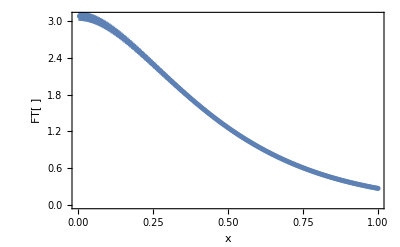

i FT[]

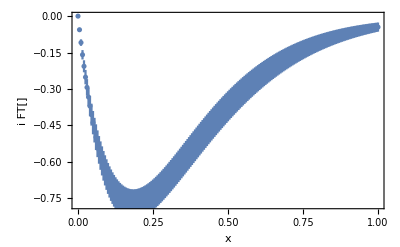

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

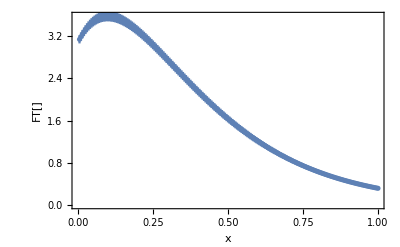

```mathematica
ParaFitA12BA2B = GiveParaFitA12BA2B[-1,7, 10, 3];
PrintxA2B[ParaFitA12BA2B,-1, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+c (1-k2/η^2-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,f,k1,k2,j} | {⟨4.01(58)⟩_(2902J), ⟨0.146(51)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨0.496(12)⟩_(2902J), ⟨12.27(50)⟩_(2902J), ⟨-36.2(28)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.56788

Fix f = 0.495907

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+c (1-k2/η^2-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,k1,k2,j} | {⟨4.03(40)⟩_(2902J), ⟨0.145(51)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨12.31(43)⟩_(2902J), ⟨-36.4(25)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.62168
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.153(31)⟩_(2902J), ⟨0.0345(56)⟩_(2902J), ⟨0.0345(56)⟩_(2902J)} | 1.47339

Infinity

FT[  ]

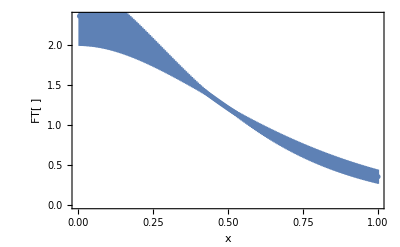

i FT[]

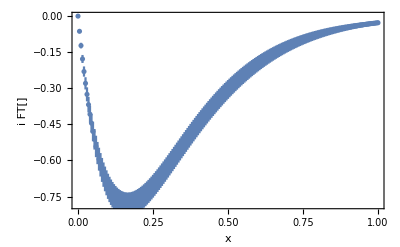

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

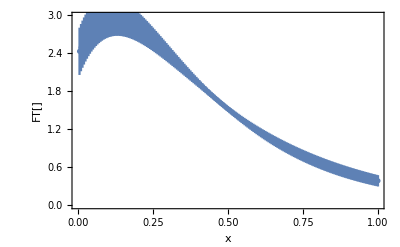

```mathematica
ParaFitA12BA2B = GiveParaFitA12BA2B[-1,6, 10, 3];
PrintxA2B[ParaFitA12BA2B,-1, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+c (1-k2/η^2-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,f,k1,k2,j} | {⟨3.12(80)⟩_(2902J), ⟨0.068(50)⟩_(2902J), ⟨0.045(19)⟩_(2902J), ⟨0.519(23)⟩_(2902J), ⟨11.9(11)⟩_(2902J), ⟨-34.5(67)⟩_(2902J), ⟨3.15(67)⟩_(2902J)} | 1.02425

Fix f = 0.519103

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+c (1-k2/η^2-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,k1,k2,j} | {⟨3.18(48)⟩_(2902J), ⟨0.066(49)⟩_(2902J), ⟨0.045(18)⟩_(2902J), ⟨12.0(11)⟩_(2902J), ⟨-34.9(65)⟩_(2902J), ⟨3.16(66)⟩_(2902J)} | 1.04299
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.266(57)⟩_(2902J), ⟨0.0362(60)⟩_(2902J), ⟨0.0362(60)⟩_(2902J)} | 1.59981

Infinity

FT[  ]

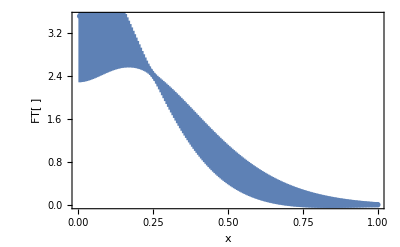

i FT[]

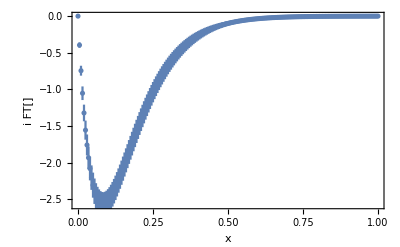

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

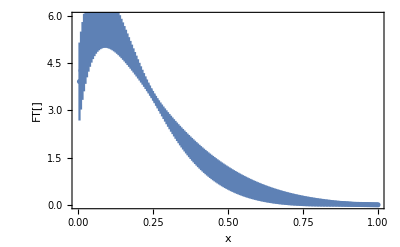

```mathematica
ParaFitA12BA2BP2 = GiveParaFitA12BA2B[-2,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP2,-2, 9]
```

3 are SELECTED for fit!

510 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+c (1-k2/η^2-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,f,k1,k2,j} | {⟨1.50(44)⟩_(2902J), ⟨0.026(31)⟩_(2902J), ⟨0.009 ± 0.011⟩_(2902J), ⟨0.503(37)⟩_(2902J), ⟨10.1(10)⟩_(2902J), ⟨-25.7(49)⟩_(2902J), ⟨1.7(84)⟩_(2902J)} | 0.990872

Fix f = 0.503419

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+c (1-k2/η^2-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,k1,k2,j} | {⟨1.54(22)⟩_(2902J), ⟨0.025(32)⟩_(2902J), ⟨0.009 ± 0.011⟩_(2902J), ⟨10.17(99)⟩_(2902J), ⟨-25.9(48)⟩_(2902J), ⟨1.8(83)⟩_(2902J)} | 0.993858
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.218(54)⟩_(2902J), ⟨0.0331(65)⟩_(2902J), ⟨0.0331(65)⟩_(2902J)} | 1.01193

Infinity

FT[  ]

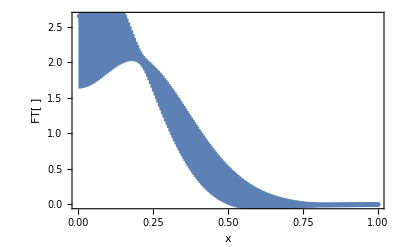

i FT[]

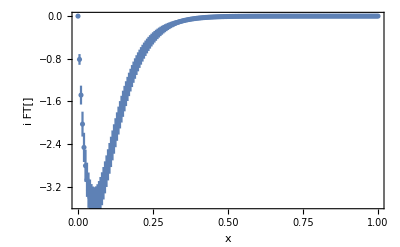

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

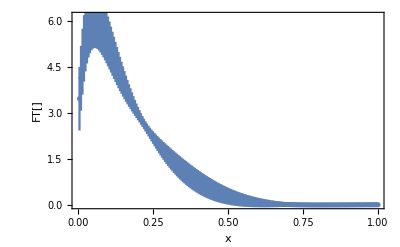

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,5, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

```mathematica
ParaFitA12BA2BP4 = GiveParaFitA12BA2B[-4,5, 10, 3];
PrintxA2B[ParaFitA12BA2BP4,-4, 9]
```

3 are SELECTED for fit!

510 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+c (1-k2/η^2-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,f,k1,k2,j} |                                                                                                                                                                                                                                                                               3
{⟨0.75(45)⟩_(2902J), ⟨-0.0522(58)⟩_(2902J), ⟨-0.00671(74)⟩_(2902J), ⟨0.445(70)⟩_(2902J), ⟨10.81(52)⟩_(2902J), ⟨-29.7(24)⟩_(2902J), ⟨582(46) × 10 ⟩_(2902J)} | 0.493899

Fix f = 0.444911

$Aborted

Infinity

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

```mathematica
ParaFitA12BA2B = GiveParaFitA12BA2B[-1,6, 10, 3];
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+c (1-k2/η^3-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,f,k1,k2,j} | {⟨4.01(58)⟩_(2902J), ⟨0.114(39)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨0.496(12)⟩_(2902J), ⟨9.41(38)⟩_(2902J), ⟨-112(11)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.56729

Fix f = 0.495913

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+c (1-k2/η^3-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,k1,k2,j} | {⟨4.03(40)⟩_(2902J), ⟨0.114(39)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨9.45(32)⟩_(2902J), ⟨-112.6(96)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.62105
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.153(31)⟩_(2902J), ⟨0.0345(56)⟩_(2902J), ⟨0.0345(56)⟩_(2902J)} | 1.47338

Infinity

FT[  ]

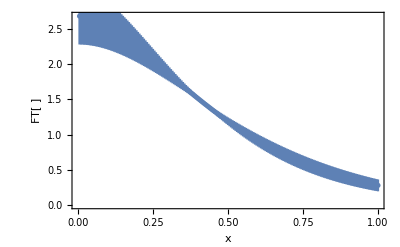

i FT[]

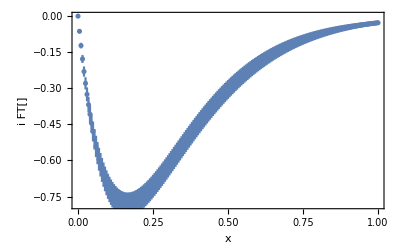

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

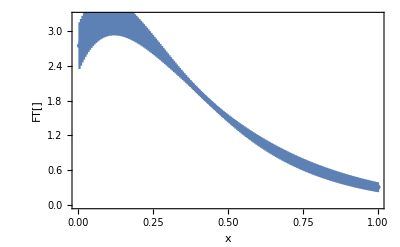

```mathematica
PrintxA2B[ParaFitA12BA2B,-1, 9]
```

```mathematica
ParaFitA12BA2B = GiveParaFitA12BA2B[-2,6, 10, 3];
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+c (1-k2/η^3-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,f,k1,k2,j} | {⟨3.13(80)⟩_(2902J), ⟨0.054(38)⟩_(2902J), ⟨0.045(19)⟩_(2902J), ⟨0.519(23)⟩_(2902J), ⟨9.07(73)⟩_(2902J), ⟨-103(25)⟩_(2902J), ⟨3.15(67)⟩_(2902J)} | 1.02477

Fix f = 0.519227

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+c (1-k2/η^3-k1/η) b_L^2+d (b_L^2+b_T^2))^-j | {a,c,d,k1,k2,j} | {⟨3.19(48)⟩_(2902J), ⟨0.053(36)⟩_(2902J), ⟨0.045(18)⟩_(2902J), ⟨9.18(68)⟩_(2902J), ⟨-105(25)⟩_(2902J), ⟨3.16(66)⟩_(2902J)} | 1.04354
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.266(57)⟩_(2902J), ⟨0.0362(60)⟩_(2902J), ⟨0.0362(60)⟩_(2902J)} | 1.59935